# Ricker model - single transient simulations of truncated population (Flip / Hopf)

## Setup

```mathematica
(* Set Directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/fish_project"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};

(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* Import user-defined functions *)
Get["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/packages/my_functions/spectral_functions.wl"];
```

```mathematica
(* Figure display parameters *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={60,50,20,20};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)

numSims=5;

(* options for EWS calculation *)
detrendOp=1; (* 1 for yes, 0 for no *)
bandWidth=0.2; (* for Gaussian filtering (as a percentage) *)
rollWindow=0.25;(* for indicator calculation *)
tauVals={1,2}; (* lag times for autocorrelation *)


(* hamming window size and length *)
hamLength=10; 
hamOffset=5;
```

## Simulate Ricker Model

### Parameters

```mathematica
(* model baseline parameter values *)
k=10; (* carrying capacity *)
p=2;(* exponent for sigmoid functional response *)
h=0.75; (* half-saturation rate *)
r=0.75; (* growth rate *)
f=0; (* grazing rate *)
x0=10; (* initial condition *)
se=0.05;(* environmental noise *)
tmax=1000; (* number of time steps *)
```

```mathematica
(* set up array for series data *)
expSeries=ConstantArray[0,{numSims,tmax+1}];
trunSeries=ConstantArray[0,{numSims,tmax+1}];
```

### Discrete dynamical system

```mathematica
(* N_t+1 = f(N_t) *)
Clear[fun]
fun[r_,k_,f_,h_,noise_,pop_]:=pop*Exp[r(1-pop/k)+se noise]-f pop^2 / (pop^2+h^2)
```

### Simulate truncation scenario

```mathematica
(* set grazing rate and exploitation fate *)
f=0;
rVals=Subdivide[0.5,2.6,tmax];
```

```mathematica
For[i=1,i≤numSims,i++,
(* array for trajectory *)
x=ConstantArray[0,tmax+1];
(* set initial condition *)
x[[1]]=10;
(* normal random variables mean zero variance 1 for noise *)
noise=RandomVariate[NormalDistribution[0,1],tmax];
(* begin simulation *)
For[q=1,q≤tmax,q++,
r=rVals[[q]];
x[[q+1]]=fun[r,k,f,h,noise[[q]],x[[q]]];
(* don't let x go negative *)
If[x[[q+1]]<0,
x[[q+1]]=0;];
];
(* add trajectory to series array *)
trunSeries[[i,;;]]=x;
]
```

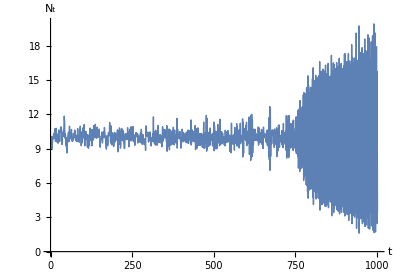

```mathematica
(* single realisation plot *)
plotSingleTrun=ListLinePlot[trunSeries[[1]],
ImageSize->400,
AspectRatio->0.7,
PlotStyle->Thickness[0.0025],
PlotRange->{0,20},
LabelStyle->14,
AxesLabel->{"t","N_t"}]
```

## Truncation scenario - traditional EWS

### Key values / parameters

```mathematica
(* control parameter range *)
rl=0.5;
rh=2.6;
(* PD bifurcation values *)
rcrit1=2; 
rcrit2=2.526;
(* transition times *)
tcritTrun=Floor[(rcrit1-rl)*tmax /(rh-rl)];

(* plot parameters *)
aHeadSize=0.03;
```

### Detrending Process (Gaussian Filter)

```mathematica
(* Detrend data up to transition *) 
tVals=Range[1,tmax];
dataFitTrunFull=If[detrendOp==1,
Table[
GaussianFilter[trunSeries[[i]],Length[tVals]*bandWidth],
{i,1,numSims}],
ConstantArray[0,{numSims,Length[tVals]}]
];
```

```mathematica
dataFitTrunFull//Dimensions
```

{5,1001}

```mathematica
dataFitTrun=dataFitTrunFull[[;;,1;;tcritTrun]];
```

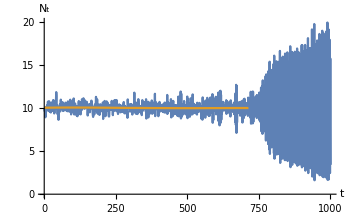

```mathematica
(* plot of single realisation *)
plotNum=1;
ListLinePlot[{trunSeries[[plotNum]],dataFitTrun[[plotNum]]},
ImageSize->350,
LabelStyle->14,
AxesLabel->{"t","N_t"},
PlotRange->{{0,tmax},{0,20}},
PlotStyle->{Default,Default},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

```mathematica
dataFitTrun//Dimensions
```

{5,714}

```mathematica
trunSeries[[;;,1;;tcritTrun]]//Dimensions
```

{5,714}

```mathematica
(* compute residuals of series *)
residualsTrun=trunSeries[[1;;numSims,1;;tcritTrun]]-dataFitTrun;
```

### Variance

```mathematica
(* number of component in the rolling window *)
windowComps=Floor[rollWindow*Length[tVals]];

(* compute variance of residuals - has form [v1;v2;v3;...;vn] *)
varSeriesTrun=Table[MovingMap[Variance,residualsTrun[[i]],windowComps],{i,1,numSims}];
varSeriesTrun//Dimensions
```

{5,464}

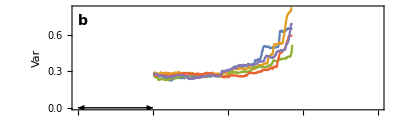

```mathematica
(* plot individual realisations *)
varPlotTrun=ListPlot[Table[{tVals[[windowComps+1;;tcritTrun]],varSeriesTrun[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},All},
FrameLabel->{{"Var",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
(*FrameTicks->{{{{0,0},{0.0005,0.5},{0.001,1},{0.0015,1.5}},Automatic},{Automatic,Automatic}},*)
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps,0}]}],
(*Text[Style["×10^-3",14],indexPos],*)
Text[Style["b",14,Bold],Scaled[labelLetterPos]]}]
```

### Coefficient of variation

```mathematica
(* compute variance of residuals - has form [v1;v2;v3;...;vn] *)
meanSeriesTrun=Table[MovingMap[Mean,trunSeries[[i,1;;tcritTrun]],windowComps],{i,1,numSims}];
meanSeriesTrun//Dimensions
```

{5,464}

```mathematica
cvSeriesTrun=Table[Sqrt[varSeriesTrun[[i]]]/meanSeriesTrun[[i]],{i,1,numSims}];
cvSeriesTrun//Dimensions
```

{5,464}

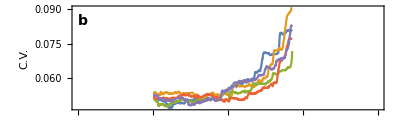

```mathematica
(* plot individual realisations *)
cvPlotTrun=ListPlot[Table[{tVals[[windowComps+1;;tcritTrun]],cvSeriesTrun[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},All},
FrameLabel->{{"C.V.",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
(*FrameTicks->{{{{0,0},{0.0005,0.5},{0.001,1},{0.0015,1.5}},Automatic},{Automatic,Automatic}},*)
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps,0}]}],
(*Text[Style["×10^-3",14],indexPos],*)
Text[Style["b",14,Bold],Scaled[labelLetterPos]]}]
```

### Autocorrelation of Residuals at lag 1

```mathematica
(* form [a1;a2;,,,;an] *)
acSeriesTrun=Table[MovingMap[CorrelationFunction[#,1]&,residualsTrun[[i]],windowComps],{i,1,numSims}];  
acSeriesTrun//Dimensions
(* sim number,time value *)
```

{5,464}

```mathematica
tVals[[windowComps+1;;]]//Dimensions
```

{750}

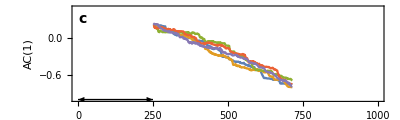

```mathematica
(* ac-1 plot of single realisations *)
acPlotTrun=ListPlot[Table[{tVals[[windowComps+1;;tcritTrun]],acSeriesTrun[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
LabelStyle->14,
Frame->True,
FrameLabel->{{"AC(1)",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{-1,0.5}},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,-1 (* yorigin value *)}],Scaled[{0,arHeight},{windowComps,-1 (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

## Power Spectrum EWS

### Compute power spectrum over rolling window with same offset has Hamming windows

```mathematica
(* evaluate power spectrum of residuals in rolling window with the offset the same as hamOffset *)
pSpecSeriesTrun=Table[MovingMap[TBPowerSpecWelch[{#,1,hamLength,hamOffset}]&,residualsTrun[[i]],{windowComps,Left,hamOffset}],{i,1,numSims}];
```

```mathematica
(* frequncy values of power spectra *)
ωVals=pSpecSeriesTrun[[1,1,1]];
```

```mathematica
pSpecSeriesTrun//Dimensions
```

{5,93,2,11}

```mathematica
(* extend the power spectrum using periodicity *)
ωExt=Join[ωVals-2Pi,ωVals,ωVals+2Pi];
psdExtend=Table[Join[pSpecSeriesTrun[[i,j,2]],pSpecSeriesTrun[[i,j,2]],pSpecSeriesTrun[[i,j,2]]],{i,1,numSims},{j,1,Dimensions[pSpecSeriesTrun][[2]]}];
trimVals=7;;-7; (* trim the domain of the power spectrum to include relevant values *)
```

```mathematica
psdExtend//Dimensions
```

{5,93,33}

### Plot of individual realisations

```mathematica
(* plot times to use *)
specTimeSpacing=2;
plotTimes=Range[1*windowComps+hamOffset,tcritTrun,specTimeSpacing*hamOffset]
```

{255,265,275,285,295,305,315,325,335,345,355,365,375,385,395,405,415,425,435,445,455,465,475,485,495,505,515,525,535,545,555,565,575,585,595,605,615,625,635,645,655,665,675,685,695,705}

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{"TemperatureMap",timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

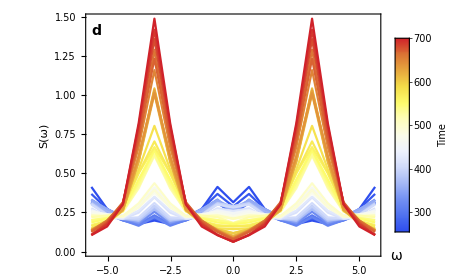

```mathematica
(* normalise to map to a colour *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
psdSinglePlotTrun=ListLinePlot[
Table[
Transpose[{ωExt[[trimVals]],psdExtend[[3,tindex]][[trimVals]]}],{tindex,1,specTimeSpacing*Length[plotTimes],specTimeSpacing}],
PlotRange->All,
PlotStyle->Thread@{ColorData["TemperatureMap"]/@plotTimesUnit},
LabelStyle->13,
Frame->True,
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.7,
FrameLabel->{{"S(ω)",None},{None,None}},
PlotRangeClipping->False,
Epilog->{(*Text[Style["×10^-3",14],Scaled[{0.065,1.05}]],*)
Text[Style["d",14,Bold],Scaled[{0.035,0.93}]],
Text[Style["ω",14],Scaled[{1.05,0}]]},
(*FrameTicks->{{Transpose[{Range[0,5,0.5]*10^(-3),Range[0,5,0.5]}],Automatic},{Automatic,Automatic}},*)
PlotLegends->Placed[colLegend,Scaled[{0.9,0.55}]]]
```

### Max-frequency component

```mathematica
pSpecSeriesTrun//Dimensions
```

{5,93,2,11}

```mathematica
(* Subscript[S, max] data *)
specMaxTrun=Table[Max[pSpecSeriesTrun[[i,j,2,;;]]],{i,1,numSims},{j,1,Dimensions[pSpecSeriesTrun][[2]]}];
specMaxTrun//Dimensions
```

{5,93}

```mathematica
tVals[[windowComps+1;;tcritTrun;;hamOffset]]//Dimensions
```

{93}

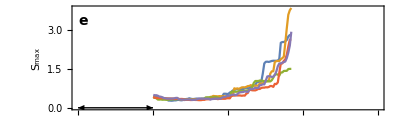

```mathematica
(* plot individual realisations *)
specMaxPlotTrun=ListPlot[Table[{tVals[[windowComps+1;;tcritTrun;;hamOffset]],specMaxTrun[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},All},
FrameLabel->{{"S_max",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
(*FrameTicks->{{Transpose[{10^(-3)*Range[0,10],Range[0,10]}],Automatic},{Automatic,Automatic}},*)
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps,0}]}],
(*Text[Style["×10^-3",14],indexPos],*)
Text[Style["e",14,Bold],Scaled[labelLetterPos]]}]
```

### Hopf-AIC weight

```mathematica
?TBHopfAIC
```

TBHopfAIC[pSpec] fits the analytical forms for the Hopf and Fold bifurcation to the data in pSpec. 
It then outputs the AIC weight that corresponds to the Hopf fit. 
Note the Hopf fit is restricted such that S(ω_0)> 2 S(0). This stops the model being selected for the Fold spectrum.
pSpec = {freqVals,powerVals}
Outputs = hopfAICweight
AIC weights can be interpreted as the probability that the fitted model is the best model (in the AIC sense)

```mathematica
pSpecSeriesTrun//Dimensions
```

{5,93,2,11}

```mathematica
Timing[TBFitSpec[pSpecSeriesTrun[[1,10]]]]
```

{0.069439,{0.980291,3.07565×10^-9,0.0197091}}

```mathematica
(* compute AIC weights - LONG SIMULATION *)
aicWeightSeriesTrun=Monitor[
Table[Quiet[TBFitSpec[pSpecSeriesTrun[[i,j]]]],{i,1,numSims},{j,1,Dimensions[pSpecSeriesTrun]⟦2⟧}],
{ProgressIndicator[i,{1,numSims}],ProgressIndicator[j,{1,Dimensions[pSpecSeriesTrun]⟦2⟧}]}];
```

```mathematica
aicWeightSeriesTrun//Dimensions
```

{5,93,3}

```mathematica
(* plot of individual realisations for wfold *)
aicFoldPlotTrun=ListPlot[Table[
{tVals[[windowComps+1;;tcritTrun;;hamOffset]],aicWeightSeriesTrun[[i,;;,1]]}ᵀ,{i,{1,2,3}}],
Joined->True,
LabelStyle->14,
PlotRange->{{0,tmax},{-0.05,1.05}},
PlotStyle->TMBcolours[[1]],
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameLabel->{{"w_fold",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{All,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps,0}]}],
Text[Style["f",14,Bold],Scaled[labelLetterPos]]}];
```

```mathematica
(* plot of individual realisations for whopf *)
aicHopfPlotTrun=ListPlot[Table[
{tVals[[windowComps+1;;tcritTrun;;hamOffset]],aicWeightSeriesTrun[[i,;;,2]]}ᵀ,{i,{1,2,3}}],
Joined->True,
LabelStyle->14,
PlotStyle->TMBcolours[[4]],
PlotRange->{{0,tmax},{-0.05,1.05}},
Frame->{{False,True},{False,False}},
FrameStyle->{Automatic,Automatic,Automatic,TMBcolours[[4]]},
FrameLabel->{{"","w_hopf"},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{None,Range[0,1,0.2]},{None,None}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3];
```

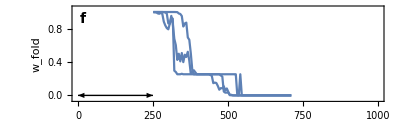
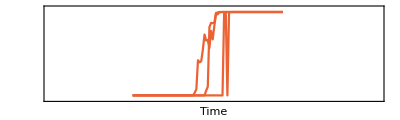

```mathematica
aicPlotTrun=Overlay[{aicFoldPlotTrun,aicHopfPlotTrun}]
```

## Bifurcation Diagram (truncated growth)

Deterministic model is
N_(t+1)=N_t e^(r(1-N_t/K))-F N_t^2/(N_t^2+h^2)

### Specifications

```mathematica
(* Import data *)
rawdata=Import["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/fish_project/bifurcation/fish_trun.dat"];

(* plotting spec *)
lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{0,3},{0,20}}; (* plot range *)
(*frLabel={"F","N"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{1lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of F *)
rbifVals=fulldata[[;;,1]];
tbifVals=(rbifVals-rl)*tmax /(rh-rl);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
nodeSections[[8]]=Cases[nodeSections[[8]],{x_,_,_,_}/; x<999] ; 
nodeSections[[10]]=Cases[nodeSections[[10]],{x_,_,_,_}/; x<999];
(* had to seperate out branches for plotting purposes *)
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}]
```

{2,1,2,1,2,1,2,1,2,1}

```mathematica
(* Take relevant branches of node sections *)
delList={5,7};
branchesNums=Complement[Range[1,numBranches],delList]
```

{1,2,3,4,6,8,9,10}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

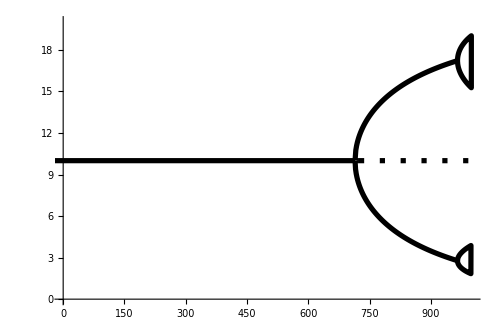

```mathematica
(* Make plot *)
bifPlotTrun=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,tmax},{0,20}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

### Output

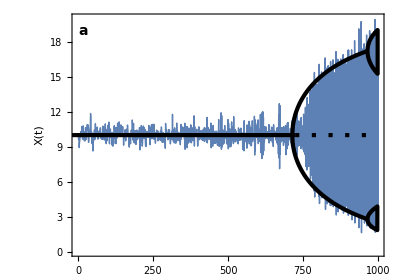

```mathematica
(* Incorporate with simulation and region of psd computation *)
lineStyle={Red,Opacity[0.4]};
sqHeight=0.12;
trajVal=0.7;

bifTrajTrun=Show[{plotSingleTrun,bifPlotTrun},
PlotRange->{{0,tmax},{0,20}},
LabelStyle->14,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"X(t)",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["a",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle]}
]
```

## Combined Plot

```mathematica
ewsPlot=Grid[{{bifTrajTrun,psdSinglePlotTrun},{varPlotTrun,specMaxPlotTrun},{acPlotTrun,aicPlotTrun}},Spacings->{-2.5,0}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics--Graphics-

```mathematica
(*Export["figures/ews_ricker_single_trun_long.png",ewsPlot,ImageResolution->200];*)
```